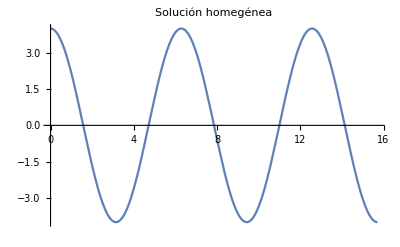

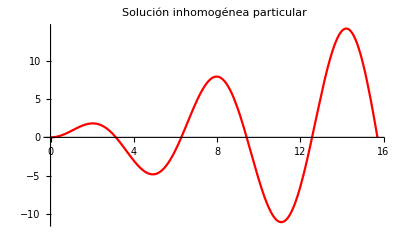

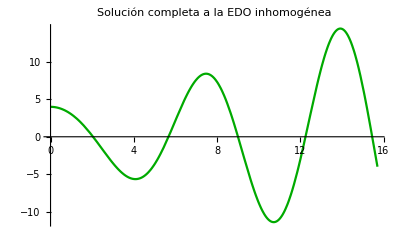

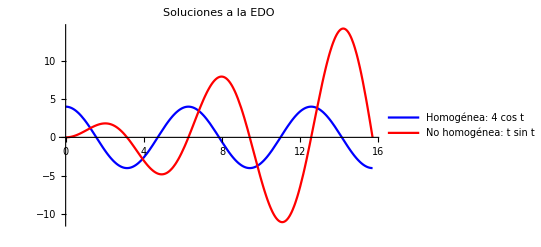

```mathematica
Plot[4 Cos [x], {x,0, 5 Pi}, PlotLabel->"Solución homegénea "]
Plot[x Sin [x], {x, 0, 5 Pi}, PlotLabel->"Solución inhomogénea particular", PlotStyle->Red]
Plot[4 Cos[x] + x Sin [x],{x,0,5 Pi}, PlotLabel->"Solución completa a la EDO inhomogénea", PlotStyle->Darker[Green]]
Plot[{4 Cos[x], x Sin[x]},{x,0, 5 Pi}, PlotLegends->{"Homogénea: 4 cos t", "No homogénea: t sin t"}, PlotLabel->"Soluciones a la EDO", PlotStyle->{Blue, Red}]
```